```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Various parameters *)
Ωγ=2.469 10^-5 h^-2;Neff=3.04;h=0.704;
Ωr=Ωγ(1+0.2271 Neff);
Mpc=3.085677 *10^22;
cH0=0.925063 *10^26;
(cH0/Mpc)/√(.13)
(* Definition of R in terms of N=Log[a] *)
Ra[Nn_]:=6(2 H[Nn]^2+H[Nn] H'[Nn])
(* Definition of the f(R) Lagrangian  *)
f[R_]:=R-2Λ (1-1/(1+(R /(b Λ))^n))/.Λ->3(1-om-or)H0^2
n=1;
```

8314.75

```mathematica
(* Definition of the ODE in terms of N=Log[a]=-Log[1+z] *)
ODE=-f'[R]H[Nn]^2+HL[Nn]^2-H0^2(1-om-or)+0(om Exp[-3 Nn]+or Exp[-4 Nn])+1/6(f'[R]R-f[R])-f''[R]H[Nn]^2 Ra'[Nn]/.R->Ra[Nn]//Simplify;
```

```mathematica
H[Nn_]:=√(HL[Nn]^2+b h1[Nn]H0^2+b^2 h2[Nn]H0^2)
```

```mathematica
s0=Series[ODE,{b,0,2}]
```

(-H0^2 h1[Nn]-(H0^4 (-1+om+or)^2)/(HL[Nn] (2 HL[Nn]+HL'[Nn]))+(2 H0^4 (-1+om+or)^2 HL[Nn]^2)/((-4 HL[Nn]^2-2 HL[Nn] HL'[Nn])^2)-(H0^4 (-1+om+or)^2 (4 HL[Nn] HL'[Nn]+HL'[Nn]^2+HL[Nn] HL''[Nn]))/(HL[Nn] (2 HL[Nn]+HL'[Nn])^3)) b+(-H0^2 h2[Nn]+(H0^6 (-1+om+or)^2 (-1+om+or-4 h1[Nn]-h1'[Nn]))/(2 HL[Nn] (2 HL[Nn]+HL'[Nn])^3)-(H0^6 (-1+om+or)^2 (-3+3 om+3 or-8 h1[Nn]-2 h1'[Nn]))/(4 HL[Nn]^2 (2 HL[Nn]+HL'[Nn])^2)+(2 H0^6 (-1+om+or)^2 h1[Nn])/((-4 HL[Nn]^2-2 HL[Nn] HL'[Nn])^2)+8 H0^4 (-1+om+or)^2 ((H0^2 HL[Nn]^2 (4 h1'[Nn]+h1''[Nn]))/(2 (-4 HL[Nn]^2-2 HL[Nn] HL'[Nn])^3)+(-(3 HL[Nn]^2 (-H0^2+H0^2 om+H0^2 or-4 H0^2 h1[Nn]-H0^2 h1'[Nn]))/((-4 HL[Nn]^2-2 HL[Nn] HL'[Nn])^4)+(H0^2 h1[Nn])/((-4 HL[Nn]^2-2 HL[Nn] HL'[Nn])^3)) (HL'[Nn]^2+HL[Nn] (4 HL'[Nn]+HL''[Nn])))) b^2+O[b]^3

```mathematica
Solve[SeriesCoefficient[s0,1]==0,h1[Nn]]//FullSimplify
```

{{h1[Nn]→-(H0^2 (-1+om+or)^2 (6 HL[Nn]^2+4 HL'[Nn]^2+HL[Nn] (15 HL'[Nn]+2 HL''[Nn])))/(2 HL[Nn] (2 HL[Nn]+HL'[Nn])^3)}}

```mathematica
h1[Nn_]:=-(H0^2 (-1+om+or)^2 (6 HL[Nn]^2+4 HL'[Nn]^2+HL[Nn] (15 HL'[Nn]+2 HL''[Nn])))/(2 HL[Nn] (2 HL[Nn]+HL'[Nn])^3)
```

```mathematica
h1[Nn]
```

-(H0^2 (-1+om+or)^2 (6 HL[Nn]^2+4 HL'[Nn]^2+HL[Nn] (15 HL'[Nn]+2 HL''[Nn])))/(2 HL[Nn] (2 HL[Nn]+HL'[Nn])^3)

```mathematica
s1=s0//Simplify//Normal
```

1/4 b^2 H0^2 (-4 h2[Nn]-(H0^6 (-1+om+or)^4 (6 HL[Nn]^2+4 HL'[Nn]^2+HL[Nn] (15 HL'[Nn]+2 HL''[Nn])))/(HL[Nn]^3 (2 HL[Nn]+HL'[Nn])^5)+(2 H0^4 (-1+om+or)^3 (16 HL[Nn]^6+32 HL[Nn]^5 HL'[Nn]-2 H0^2 (-1+om+or) HL'[Nn]^4+24 HL[Nn]^4 (H0^2 (-1+om+or)+HL'[Nn]^2)-2 H0^2 (-1+om+or) HL[Nn] HL'[Nn]^2 (4 HL'[Nn]+HL''[Nn])+HL[Nn]^2 (4 H0^2 (-1+om+or) HL'[Nn]^2+HL'[Nn]^4-3 H0^2 (-1+om+or) HL''[Nn]^2-H0^2 (-1+om+or) HL'[Nn] (9 HL''[Nn]-HL^(3)[Nn]))+2 HL[Nn]^3 (30 H0^2 (-1+om+or) HL'[Nn]+4 HL'[Nn]^3+H0^2 (-1+om+or) (7 HL''[Nn]+HL^(3)[Nn]))))/(HL[Nn]^3 (2 HL[Nn]+HL'[Nn])^7)-(H0^4 (-1+om+or)^3 (48 HL[Nn]^6+96 HL[Nn]^5 HL'[Nn]-4 H0^2 (-1+om+or) HL'[Nn]^4+24 HL[Nn]^4 (2 H0^2 (-1+om+or)+3 HL'[Nn]^2)-4 H0^2 (-1+om+or) HL[Nn] HL'[Nn]^2 (4 HL'[Nn]+HL''[Nn])+HL[Nn]^2 (8 H0^2 (-1+om+or) HL'[Nn]^2+3 HL'[Nn]^4-6 H0^2 (-1+om+or) HL''[Nn]^2-2 H0^2 (-1+om+or) HL'[Nn] (9 HL''[Nn]-HL^(3)[Nn]))+4 HL[Nn]^3 (30 H0^2 (-1+om+or) HL'[Nn]+6 HL'[Nn]^3+H0^2 (-1+om+or) (7 HL''[Nn]+HL^(3)[Nn]))))/(HL[Nn]^4 (2 HL[Nn]+HL'[Nn])^6)-(2 H0^4 (-1+om+or)^3 (-14 H0^2 (-1+om+or) HL'[Nn]^6+48 HL[Nn]^7 (4 HL'[Nn]+HL''[Nn])+48 HL[Nn]^6 HL'[Nn] (9 HL'[Nn]+2 HL''[Nn])-H0^2 (-1+om+or) HL[Nn] HL'[Nn]^4 (127 HL'[Nn]+20 HL''[Nn])+HL[Nn]^2 HL'[Nn]^2 (-370 H0^2 (-1+om+or) HL'[Nn]^2+3 HL'[Nn]^4-21 H0^2 (-1+om+or) HL''[Nn]^2-H0^2 (-1+om+or) HL'[Nn] (134 HL''[Nn]-5 HL^(3)[Nn]))+4 HL[Nn]^5 (72 H0^2 (-1+om+or) HL'[Nn]+96 HL'[Nn]^3+18 HL'[Nn]^2 HL''[Nn]+H0^2 (-1+om+or) (6 HL''[Nn]-7 HL^(3)[Nn]-HL^(4)[Nn]))+4 HL[Nn]^4 (186 H0^2 (-1+om+or) HL'[Nn]^2+42 HL'[Nn]^4+6 HL'[Nn]^3 HL''[Nn]+3 H0^2 (-1+om+or) HL''[Nn] (9 HL''[Nn]+2 HL^(3)[Nn])+H0^2 (-1+om+or) HL'[Nn] (120 HL''[Nn]+10 HL^(3)[Nn]-HL^(4)[Nn]))-HL[Nn]^3 (212 H0^2 (-1+om+or) HL'[Nn]^3-36 HL'[Nn]^5-3 HL'[Nn]^4 HL''[Nn]+21 H0^2 (-1+om+or) HL''[Nn]^3+6 H0^2 (-1+om+or) HL'[Nn] HL''[Nn] (19 HL''[Nn]-2 HL^(3)[Nn])+H0^2 (-1+om+or) HL'[Nn]^2 (206 HL''[Nn]-37 HL^(3)[Nn]+HL^(4)[Nn]))))/(HL[Nn]^4 (2 HL[Nn]+HL'[Nn])^8))

```mathematica
Solve[s1==0,h2[Nn]]//FullSimplify
```

{{h2[Nn]→-(H0^4 (-1+om+or)^3 (128 HL[Nn]^8-32 H0^2 (-1+om+or) HL'[Nn]^6+32 HL[Nn]^7 (25 HL'[Nn]+3 HL''[Nn])-2 H0^2 (-1+om+or) HL[Nn] HL'[Nn]^4 (139 HL'[Nn]+22 HL''[Nn])+16 HL[Nn]^6 (9 H0^2 (-1+om+or)+89 HL'[Nn]^2+12 HL'[Nn] HL''[Nn])+HL[Nn]^2 HL'[Nn]^2 (-749 H0^2 (-1+om+or) HL'[Nn]^2+9 HL'[Nn]^4-48 H0^2 (-1+om+or) HL''[Nn]^2-4 H0^2 (-1+om+or) HL'[Nn] (74 HL''[Nn]-3 HL^(3)[Nn]))+8 HL[Nn]^5 (144 H0^2 (-1+om+or) HL'[Nn]+146 HL'[Nn]^3+18 HL'[Nn]^2 HL''[Nn]+H0^2 (-1+om+or) (15 HL''[Nn]-6 HL^(3)[Nn]-HL^(4)[Nn]))+4 HL[Nn]^4 (540 H0^2 (-1+om+or) HL'[Nn]^2+124 HL'[Nn]^4+12 HL'[Nn]^3 HL''[Nn]+3 H0^2 (-1+om+or) HL''[Nn] (17 HL''[Nn]+4 HL^(3)[Nn])+2 H0^2 (-1+om+or) HL'[Nn] (129 HL''[Nn]+12 HL^(3)[Nn]-HL^(4)[Nn]))-2 HL[Nn]^3 (84 H0^2 (-1+om+or) HL'[Nn]^3-53 HL'[Nn]^5-3 HL'[Nn]^4 HL''[Nn]+21 H0^2 (-1+om+or) HL''[Nn]^3+3 H0^2 (-1+om+or) HL'[Nn] HL''[Nn] (41 HL''[Nn]-4 HL^(3)[Nn])+H0^2 (-1+om+or) HL'[Nn]^2 (217 HL''[Nn]-42 HL^(3)[Nn]+HL^(4)[Nn]))))/(4 HL[Nn]^4 (2 HL[Nn]+HL'[Nn])^8)}}

```mathematica
h2[Nn_]:=-(H0^4 (-1+om+or)^3 (128 HL[Nn]^8-32 H0^2 (-1+om+or) HL'[Nn]^6+32 HL[Nn]^7 (25 HL'[Nn]+3 HL''[Nn])-2 H0^2 (-1+om+or) HL[Nn] HL'[Nn]^4 (139 HL'[Nn]+22 HL''[Nn])+16 HL[Nn]^6 (9 H0^2 (-1+om+or)+89 HL'[Nn]^2+12 HL'[Nn] HL''[Nn])+HL[Nn]^2 HL'[Nn]^2 (-749 H0^2 (-1+om+or) HL'[Nn]^2+9 HL'[Nn]^4-48 H0^2 (-1+om+or) HL''[Nn]^2-4 H0^2 (-1+om+or) HL'[Nn] (74 HL''[Nn]-3 Derivative[3][HL][Nn]))+8 HL[Nn]^5 (144 H0^2 (-1+om+or) HL'[Nn]+146 HL'[Nn]^3+18 HL'[Nn]^2 HL''[Nn]+H0^2 (-1+om+or) (15 HL''[Nn]-6 Derivative[3][HL][Nn]-Derivative[4][HL][Nn]))+4 HL[Nn]^4 (540 H0^2 (-1+om+or) HL'[Nn]^2+124 HL'[Nn]^4+12 HL'[Nn]^3 HL''[Nn]+3 H0^2 (-1+om+or) HL''[Nn] (17 HL''[Nn]+4 Derivative[3][HL][Nn])+2 H0^2 (-1+om+or) HL'[Nn] (129 HL''[Nn]+12 Derivative[3][HL][Nn]-Derivative[4][HL][Nn]))-2 HL[Nn]^3 (84 H0^2 (-1+om+or) HL'[Nn]^3-53 HL'[Nn]^5-3 HL'[Nn]^4 HL''[Nn]+21 H0^2 (-1+om+or) HL''[Nn]^3+3 H0^2 (-1+om+or) HL'[Nn] HL''[Nn] (41 HL''[Nn]-4 Derivative[3][HL][Nn])+H0^2 (-1+om+or) HL'[Nn]^2 (217 HL''[Nn]-42 Derivative[3][HL][Nn]+Derivative[4][HL][Nn]))))/(4 HL[Nn]^4 (2 HL[Nn]+HL'[Nn])^8)
```

```mathematica
h2[Nn]//FullSimplify
```

-(H0^4 (-1+om+or)^3 (128 HL[Nn]^8-32 H0^2 (-1+om+or) HL'[Nn]^6+32 HL[Nn]^7 (25 HL'[Nn]+3 HL''[Nn])-2 H0^2 (-1+om+or) HL[Nn] HL'[Nn]^4 (139 HL'[Nn]+22 HL''[Nn])+16 HL[Nn]^6 (9 H0^2 (-1+om+or)+89 HL'[Nn]^2+12 HL'[Nn] HL''[Nn])+HL[Nn]^2 HL'[Nn]^2 (-749 H0^2 (-1+om+or) HL'[Nn]^2+9 HL'[Nn]^4-48 H0^2 (-1+om+or) HL''[Nn]^2-4 H0^2 (-1+om+or) HL'[Nn] (74 HL''[Nn]-3 HL^(3)[Nn]))+8 HL[Nn]^5 (144 H0^2 (-1+om+or) HL'[Nn]+146 HL'[Nn]^3+18 HL'[Nn]^2 HL''[Nn]+H0^2 (-1+om+or) (15 HL''[Nn]-6 HL^(3)[Nn]-HL^(4)[Nn]))+4 HL[Nn]^4 (540 H0^2 (-1+om+or) HL'[Nn]^2+124 HL'[Nn]^4+12 HL'[Nn]^3 HL''[Nn]+3 H0^2 (-1+om+or) HL''[Nn] (17 HL''[Nn]+4 HL^(3)[Nn])+2 H0^2 (-1+om+or) HL'[Nn] (129 HL''[Nn]+12 HL^(3)[Nn]-HL^(4)[Nn]))-2 HL[Nn]^3 (84 H0^2 (-1+om+or) HL'[Nn]^3-53 HL'[Nn]^5-3 HL'[Nn]^4 HL''[Nn]+21 H0^2 (-1+om+or) HL''[Nn]^3+3 H0^2 (-1+om+or) HL'[Nn] HL''[Nn] (41 HL''[Nn]-4 HL^(3)[Nn])+H0^2 (-1+om+or) HL'[Nn]^2 (217 HL''[Nn]-42 HL^(3)[Nn]+HL^(4)[Nn]))))/(4 HL[Nn]^4 (2 HL[Nn]+HL'[Nn])^8)

```mathematica
HL[Nn_]:=H0 √(om Exp[-3 Nn]+or Exp[-4 Nn]+(1-om-or))
```

```mathematica
H[Nn]//Simplify
```

√(H0^2 (1+(-1+ⅇ^(-3 Nn)) om+(-1+ⅇ^(-4 Nn)) or+(2 b ⅇ^(2 Nn) (-1+om+or)^2 (-6 ⅇ^Nn om^2-7 om or+3 ⅇ^(4 Nn) om (-1+om+or)+4 ⅇ^(3 Nn) or (-1+om+or)+12 ⅇ^(7 Nn) (-1+om+or)^2))/(-om+4 ⅇ^(3 Nn) (-1+om+or))^3+(b^2 ⅇ^(5 Nn) (-1+om+or)^3 (37 ⅇ^Nn om^6+40 om^5 or-4656 ⅇ^(4 Nn) om^5 (-1+om+or)-8692 ⅇ^(3 Nn) om^4 or (-1+om+or)-4032 ⅇ^(2 Nn) om^3 or^2 (-1+om+or)-7452 ⅇ^(7 Nn) om^4 (-1+om+or)^2-25728 ⅇ^(6 Nn) om^3 or (-1+om+or)^2-17856 ⅇ^(5 Nn) om^2 or^2 (-1+om+or)^2+25408 ⅇ^(10 Nn) om^3 (-1+om+or)^3+22016 ⅇ^(9 Nn) om^2 or (-1+om+or)^3-9216 ⅇ^(8 Nn) om or^2 (-1+om+or)^3-22848 ⅇ^(13 Nn) om^2 (-1+om+or)^4-2048 ⅇ^(12 Nn) om or (-1+om+or)^4+9216 ⅇ^(16 Nn) om (-1+om+or)^5+3072 ⅇ^(15 Nn) or (-1+om+or)^5+1024 ⅇ^(19 Nn) (-1+om+or)^6))/(om-4 ⅇ^(3 Nn) (-1+om+or))^8))

```mathematica
H0=1;
Happrox[Nn_,b_,om_]:=√(H0^2 (1+(-1+ⅇ^(-3 Nn)) om+(-1+ⅇ^(-4 Nn)) or+(2 b ⅇ^(2 Nn) (-1+om+or)^2 (-6 ⅇ^Nn om^2-7 om or+3 ⅇ^(4 Nn) om (-1+om+or)+4 ⅇ^(3 Nn) or (-1+om+or)+12 ⅇ^(7 Nn) (-1+om+or)^2))/(-om+4 ⅇ^(3 Nn) (-1+om+or))^3+(b^2 ⅇ^(5 Nn) (-1+om+or)^3 (37 ⅇ^Nn om^6+40 om^5 or-4656 ⅇ^(4 Nn) om^5 (-1+om+or)-8692 ⅇ^(3 Nn) om^4 or (-1+om+or)-4032 ⅇ^(2 Nn) om^3 or^2 (-1+om+or)-7452 ⅇ^(7 Nn) om^4 (-1+om+or)^2-25728 ⅇ^(6 Nn) om^3 or (-1+om+or)^2-17856 ⅇ^(5 Nn) om^2 or^2 (-1+om+or)^2+25408 ⅇ^(10 Nn) om^3 (-1+om+or)^3+22016 ⅇ^(9 Nn) om^2 or (-1+om+or)^3-9216 ⅇ^(8 Nn) om or^2 (-1+om+or)^3-22848 ⅇ^(13 Nn) om^2 (-1+om+or)^4-2048 ⅇ^(12 Nn) om or (-1+om+or)^4+9216 ⅇ^(16 Nn) om (-1+om+or)^5+3072 ⅇ^(15 Nn) or (-1+om+or)^5+1024 ⅇ^(19 Nn) (-1+om+or)^6))/(om-4 ⅇ^(3 Nn) (-1+om+or))^8))/.or->Ωr
```

```mathematica
(* Solve the ODE *)
h=0.704;
or0=Ωr;
om0=.24;
Clear[H]
H0=1;
modfried[om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(modfried[om1,b1,Ns]=NDSolve[{(ODE/.om->om1/.b->b1/.or->or0//Evaluate)==0,H[Ns]==√(om0 Exp[-3 Ns]+or0 Exp[-4 Ns]+1-om0-or0),H'[Ns]==-(ⅇ^(-4 Ns) (3 ⅇ^Ns om0+4 or0))/(2 √(1+(-1+ⅇ^(-3 Ns)) om0+(-1+ⅇ^(-4 Ns)) or0))},H,{Nn,Ns,0},MaxSteps->2000000])
Hsol[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(H[Nn]/.modfried[om1,b1,Ns][[1]])
Hsolp[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(H'[Nn]/.modfried[om1,b1,Ns][[1]])
yH[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=((H[Nn]^2/om0-Exp[-3Nn]-or0/om0 Exp[-4Nn])/.modfried[om1,b1,Ns][[1]])
yHp[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=((3 ⅇ^(-3 Nn)+(4 ⅇ^(-4 Nn) or0)/om0+(2 H[Nn] H'[Nn])/om0)/.modfried[om1,b1,Ns][[1]])
```

```mathematica
Ns=Log[1/(1+30.)];
```

```mathematica
100(1-Happrox[Log[1/(1+0.1)],0.01,0.24]/Hsol[Log[1/(1+0.1)],om0,.01,Ns])
```

3.19025×10^-6

```mathematica
100(1-Happrox[Log[1/(1+0.1)],0.1,0.24]/Hsol[Log[1/(1+0.1)],om0,.1,Ns])
```

-0.0003845

```mathematica
100(1-Happrox[Log[1/(1+0.1)],1,0.24]/Hsol[Log[1/(1+0.1)],om0,1,Ns])
```

2.1157

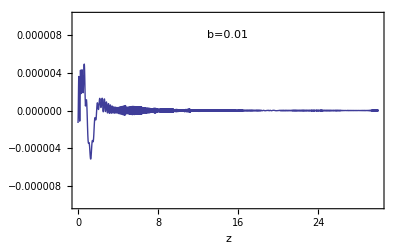

```mathematica
Plot[100(1-Happrox[Log[1/(1+z)],0.01,0.24]/Hsol[Log[1/(1+z)],om0,.01,Ns]),{z,0.,30.},PlotRange->{-0.00001,0.00001},Frame->True,FrameLabel->{"z","% diff."},Epilog->{Text["b=0.01",{15,0.000008}]}]
```

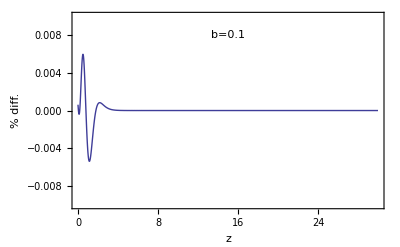

```mathematica
Plot[100(1-Happrox[Log[1/(1+z)],0.1,0.24]/Hsol[Log[1/(1+z)],om0,.1,Ns]),{z,0.,30.},PlotRange->{-0.01,0.01},Frame->True,FrameLabel->{"z","% diff."},Epilog->{Text["b=0.1",{15,0.008}]}]
```

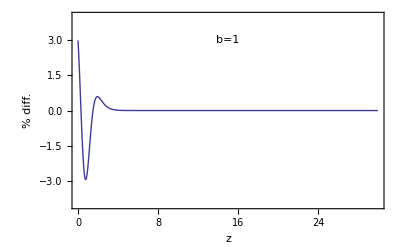

```mathematica
Plot[100(1-Happrox[Log[1/(1+z)],1,0.24]/Hsol[Log[1/(1+z)],om0,1,Ns]),{z,0.,30.},PlotRange->{-4,4},Frame->True,FrameLabel->{"z","% diff."},Epilog->{Text["b=1",{15,3}]}]
```

```mathematica
Off[NIntegrate::slwcon,NIntegrate::ncvb]
```

```mathematica
{Hsol[Log[1/(1+0.1)],om0,.01,Ns],Hsol[Log[1/(1+0.1)],om0,.02,Ns],Hsol[Log[1/(1+0.1)],om0,.05,Ns],Hsol[Log[1/(1+0.1)],om0,.1,Ns],Hsol[Log[1/(1+0.1)],om0,.2,Ns],Hsol[Log[1/(1+0.1)],om0,.3,Ns],Hsol[Log[1/(1+0.1)],om0,.4,Ns],Hsol[Log[1/(1+0.1)],om0,.5,Ns],Hsol[Log[1/(1+0.1)],om0,1,Ns],Hsol[Log[1/(1+0.1)],om0,2,Ns]}
```

{1.03816,1.03735,1.03493,1.03097,1.02355,1.01771,1.01341,1.01011,0.9988,0.975211}

```mathematica
testdatH=Table[{b,NIntegrate[100*(1-Happrox[Log[1/(1+z)],b,0.24]/Hsol[Log[1/(1+z)],om0,b,Ns]),{z,0,30}]/30//Abs},{b,{0.01,0.02,0.05,0.1,0.2,0.3,0.4,0.5,1,2}}];
```

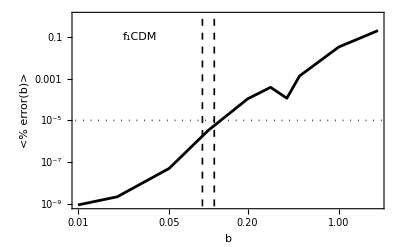

```mathematica
pl2=ListLogLogPlot[testdatH,Frame->True,Joined->True,PlotStyle->{Thickness[0.005],Black},FrameLabel->{"b","<% error(b)>"},BaseStyle->{FontSize->18,FontFamily->"Times"},Epilog->{{Dashed,Thickness[0.003],Line[{{0.09,10^-15},{0.09,2}}//Log]},{Dashed,Thickness[0.003],Line[{{0.111,10^-15},{0.111,2}}//Log]},{Dotted,Thickness[0.003],Line[{{0.001,10^-5},{10,10^-5}}//Log]},Text["f_1CDM",Log[{0.03,0.1}]]}]
```

```mathematica
Export[".\\plots\\accuracyH(z)_HS.eps",pl2,ImageSize->600]
```

.\plots\accuracyH(z)_HS.eps